```mathematica
Clear[u,a,b,d,S,B,t]
```

```mathematica
B[z_]:=1+2(Sin[π z]/π)^2(1/z-∑_(n=1)^∞ 1/(n+z)^2);
```

```mathematica
S1[d_,b_,z_]:=-1/2(B[d(-b-z)]+B[d(z-b)]);
S2[d_,b_,z_] := 1/2(B[d(b+z)]+B[d(b-z)]);

char[b_,x_] :=If[-b<x<b,1,0];

S1hat[d_, b_, x_] :=  NIntegrate[S1[d, b,t]Cos[2π t x],{t,-200,200}];

S2hat[d_, b_, x_] :=  NIntegrate[S2[d, b,t]Cos[2π t x],{t,-200,200}];

x[n_] := Log[n]/(2π);

id[b_,d_] :=If[S1hat[d,b, x[5]] ≥ 0 ,1.0 , -1.0];

Shat0S1[b_,d_] := 2b - 1/d;

Shat0S2[b_,d_] := 2b + 1/d;

digammaintegralS1[b_,d_, x_, y_]:= Re[NIntegrate[Gamma'[1/4+(ⅈ r)/2+x+y ⅈ ]/Gamma[1/4+(ⅈ r)/2+x+y ⅈ ] S1[d,b,r],{r,-200,200}]]-Log[π]Shat0S1[b,d];

digammaintegralS2[b_,d_, x_, y_]:= Re[NIntegrate[Gamma'[1/4+(ⅈ r)/2+x+y ⅈ ]/Gamma[1/4+(ⅈ r)/2+x+y ⅈ ] S2[d,b,r],{r,-200,200}]]-Log[π]Shat0S2[b,d];
eta[b_, d_] :=digammaintegralS1[b,d, 0, 0];
```

```mathematica
delta = x[2];
beta = 22.36;
```

$Aborted

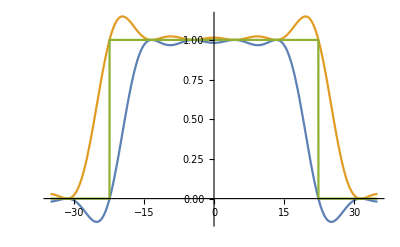

```mathematica
p1 =Plot[{S1[delta,beta,x], S2[delta,beta,x], char[beta, x]}, {x,-35,35}];
p2 = Plot[{S1hat[delta,beta,x], S2hat[delta,beta,x]}, {x,-Log[3]/(2π),Log[3]/(2π)}, PlotRange->{{-0.15,0.15},{-12,40}}];
GraphicsRow[{p1,p2}]
```

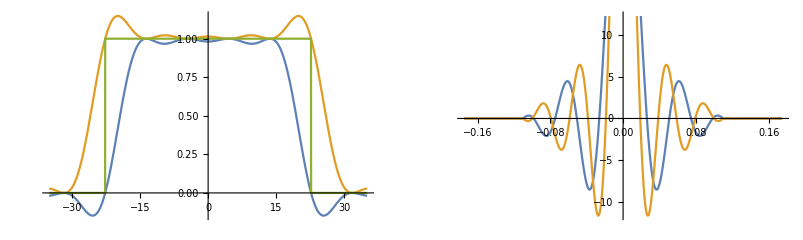

16830.3

```mathematica
x[n_] := Log[n]/(2π);

id[b_,d_] :=If[S1hat[d,b, x[5]] ≥ 0 ,1.0 , -1.0];

Shat0S1[b_,d_] := 2b - 1/d;

Shat0S2[b_,d_] := 2b + 1/d;

digammaintegralS1[b_,d_, x_, y_]:= Re[NIntegrate[Gamma'[1/4+(ⅈ r)/2+x+y ⅈ ]/Gamma[1/4+(ⅈ r)/2+x+y ⅈ ] S1[d,b,r],{r,-200,200}]]-Log[π]Shat0S1[b,d];

digammaintegralS2[b_,d_, x_, y_]:= Re[NIntegrate[Gamma'[1/4+(ⅈ r)/2+x+y ⅈ ]/Gamma[1/4+(ⅈ r)/2+x+y ⅈ ] S2[d,b,r],{r,-200,200}]]-Log[π]Shat0S2[b,d];

ListDensityPlot[Table[id[b,d],{d,Log[5]/(2π),Log[7]/(2π),(Log[7]/(2π)- Log[5]/(2π))/40},{b,17.5,23,(23-17.5)/40}],DataRange->{{17.5,23},{Log[5]/(2π),Log[7]/(2π)}}, ColorFunction->GrayLevel,PlotLegends->Automatic,MeshFunctions->{ #1*#2- 2.5 &,Function[{x,y,z}, digammaintegralS1[x,y, 0, 0]] },MeshStyle->{Lighter[Red],Lighter[Green]}, Mesh-> {{0.}}]
TimeUsed[]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {195.752}. NIntegrate obtained -0.0026902 and 5.86597×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {175.976}. NIntegrate obtained 0.0582297 and 5.91884×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {-121.778}. NIntegrate obtained 41.019+0.0000779768 ⅈ and 0.000161417 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

15157.1

```mathematica
id[20.1,x[7]]
id[20.5, x[7]]
```

-1.

1.

```mathematica
S1hat[x[7], 20.32, x[5]]
```

-0.0568374

```mathematica
S1hat[x[7], 20.5, x[5]]
```

0.106918

```mathematica
|
```

```mathematica
eta[b_, d_] :=digammaintegralS1[b,d, 0, 0];
```

```mathematica
eta[20.0, x[7]]
eta[20.5, x[7]]
```

1.12694

2.21808

```mathematica
Stot[t_] :=1/(S1hat[x[7], 20.0, x[5]]-S1hat[x[7], 20.32, x[5]]) (-S1hat[x[7], 20.32, x[5]] S1[x[7],20.5,t] + S1hat[x[7], 20.5, x[5]] S1[x[7],20.32,t]);

Stotfourier[bmin_,b_,t_] := 1/(S1hat[x[7], b, x[5]]-S1hat[x[7],bmin, x[5]]) (-S1hat[x[7], bmin, x[5]] S1hat[x[7],b,t] + S1hat[x[7], b, x[5]] S1hat[x[7],bmin,t]);

etatot[bmin_,b_] := 1/(S1hat[x[7], b, x[5]]-S1hat[x[7], bmin, x[5]]) (-S1hat[x[7], bmin, x[5]] eta[b, x[7]] + S1hat[x[7],b, x[5]] eta[bmin, x[7]]);
```

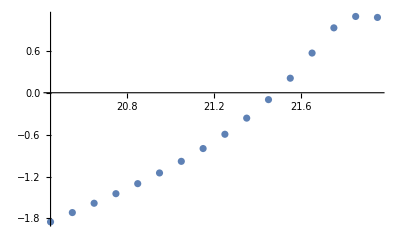

```mathematica
DiscretePlot[etatot[19.5,b]-Sqrt[2]*Log[2]Abs[Stotfourier[19.5,b,x[2]]] - 2*Log[3]/Sqrt[3] Abs[Stotfourier[19.5,b,x[3]]] - 2*Log[2]/Sqrt[4] Abs[Stotfourier[19.5,b,x[4]]], {b, 20.45, 22.0, 0.1},Filling->None]
```

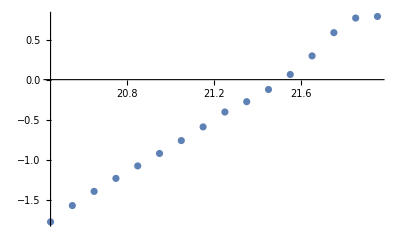

```mathematica
DiscretePlot[etatot[19,b]-Sqrt[2]*Log[2]Abs[Stotfourier[19,b,x[2]]] - 2*Log[3]/Sqrt[3] Abs[Stotfourier[19,b,x[3]]] - 2*Log[2]/Sqrt[4] Abs[Stotfourier[19,b,x[4]]], {b, 20.45, 22.0, 0.1},Filling->None]
```

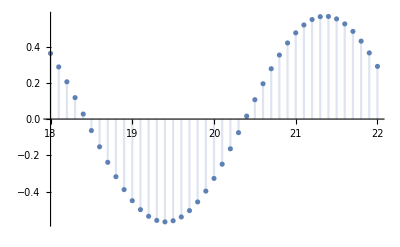

```mathematica
value[bmin_,b_]:=etatot[bmin,b]-Sqrt[2]*Log[2]Abs[Stotfourier[bmin,b,x[2]]] - 2*Log[3]/Sqrt[3] Abs[Stotfourier[bmin,b,x[3]]] - 2*Log[2]/Sqrt[4] Abs[Stotfourier[bmin,b,x[4]]];
DiscretePlot[S1hat[x[7], b, x[5]], {b, 18,22, 0.1}]
```

```mathematica
value[19.2,21.44]
```

0.0105457

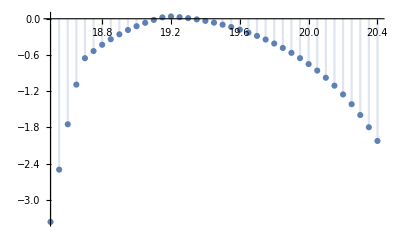

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {115.234}. NIntegrate obtained 1.86497×10^-7 and 2.30793×10^-11 for the integral and error estimates.

```mathematica
DiscretePlot[value[b,21.45], {b, 18.5, 20.4, 0.05}]
```

With log(2)/2pi:

```mathematica
id2[b_,d_] :=If[S1hat[d,b, x[2]] ≥ 0 ,1.0 , -1.0];
```

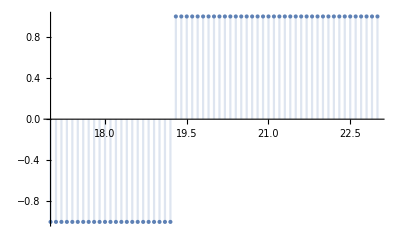

```mathematica
DiscretePlot[id2[b,x[7]], {b, 17,23,0.1}]
```

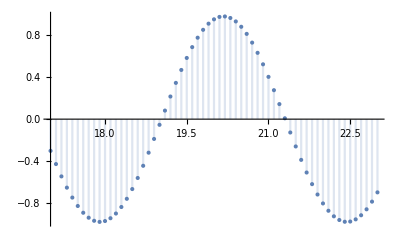

```mathematica
DiscretePlot[S1hat[x[7], b, x[4]], {b, 17,23, 0.1}]
```

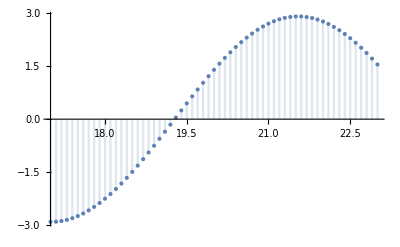

```mathematica
DiscretePlot[S1hat[x[7], b, x[2]], {b, 17,23, 0.1}]
```

```mathematica
Stotfourier[bmin_,b_,t_] := 1/(S1hat[x[7], b, x[2]]-S1hat[x[7], bmin, x[2]]) (-S1hat[x[7],bmin, x[2]] S1hat[x[7],b,t] + S1hat[x[7], b, x[2]] S1hat[x[7],bmin,t]);

etatot[bmin_,b_] := 1/(S1hat[x[7], b, x[2]]-S1hat[x[7], bmin, x[2]]) (-S1hat[x[7], bmin, x[2]] eta[b, x[7]] + S1hat[x[7],b, x[2]] eta[bmin, x[7]]);
```

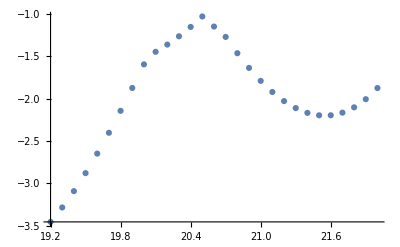

```mathematica
DiscretePlot[etatot[17.5,b]- 2*Log[3]/Sqrt[3] Abs[Stotfourier[17.5,b,x[3]]] - 2*Log[2]/Sqrt[4] Abs[Stotfourier[17.5,b,x[4]]]-  2*Log[5]/Sqrt[5] Abs[Stotfourier[17.5,b,x[5]]], {b,19.2, 22.0, 0.1},Filling->None,AxesOrigin->None ]
```

With log(3)/2pi:

```mathematica
id3[b_,d_] :=If[S1hat[d,b, x[3]] ≥ 0 ,1.0 , -1.0];
```

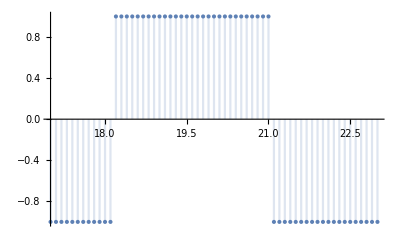

```mathematica
DiscretePlot[id3[b,x[7]], {b, 17,23,0.1}]
```

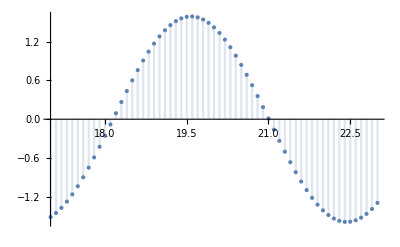

```mathematica
DiscretePlot[S1hat[x[7], b, x[3]], {b, 17,23, 0.1}]
```

```mathematica
Stotfourier[bmin_,b_,t_] := 1/(S1hat[x[7], bmin, x[3]]-S1hat[x[7], b, x[3]]) (S1hat[x[7],bmin, x[3]] S1hat[x[7],b,t] - S1hat[x[7], b, x[3]] S1hat[x[7],bmin,t]);

etatot[bmin_,b_] := 1/(S1hat[x[7], bmin, x[3]]-S1hat[x[7], b, x[3]]) (S1hat[x[7], bmin, x[3]] eta[b, x[7]] - S1hat[x[7],b, x[3]] eta[bmin, x[7]]);

etaplot[bmin_,b_]:=etatot[bmin,b]- 2*Log[2]/Sqrt[2] Abs[Stotfourier[bmin,b,x[2]]] - 2*Log[2]/Sqrt[4] Abs[Stotfourier[bmin,b,x[4]]]-  2*Log[5]/Sqrt[5] Abs[Stotfourier[bmin,b,x[5]]];
```

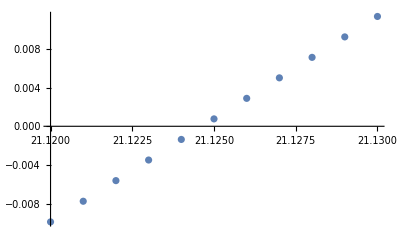

```mathematica
DiscretePlot[etaplot[18.87,b], {b,21.12, 21.13, 0.001},Filling->None,AxesOrigin->None ]
```

```mathematica
etaplot[18.87,21.125]
```

0.000764272

```mathematica
etaplotKS[bmin_,b_]:=etatot[bmin,b]- 2*Log[2]/Sqrt[2] 2^(7/64)Abs[Stotfourier[bmin,b,x[2]]] - 2*Log[2]/Sqrt[4] 2^(14/64)Abs[Stotfourier[bmin,b,x[4]]]-  2*Log[5]/Sqrt[5] 5^(7/64)Abs[Stotfourier[bmin,b,x[5]]];
```

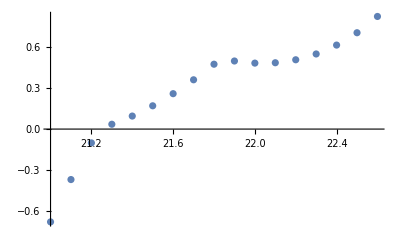

```mathematica
DiscretePlot[etaplotKS[18.87,b], {b,21, 22.6, 0.1},Filling->None,AxesOrigin->None ]
```

```mathematica
etaplotKS[18.87,21.245]
```

0.00962825

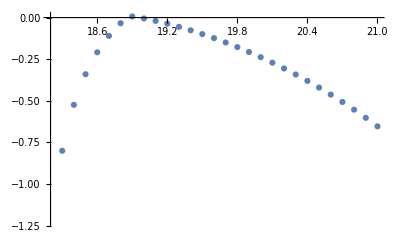

```mathematica
DiscretePlot[etaplotKS[bmin,21.245], {bmin,18.2, 21, 0.1},Filling->None,AxesOrigin->None ]
```

```mathematica
etaplotUN[bmin_,b_]:=etatot[bmin,b]- 2*Log[2]/Sqrt[2] 2^(1/2)Abs[Stotfourier[bmin,b,x[2]]] - 2*Log[2]/Sqrt[4] 2Abs[Stotfourier[bmin,b,x[4]]]-  2*Log[5]/Sqrt[5] 5^(1/2)Abs[Stotfourier[bmin,b,x[5]]];
```

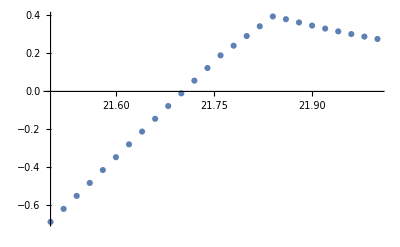

```mathematica
DiscretePlot[etaplotUN[19.7,b], {b,21.5, 22, 0.02},Filling->None,AxesOrigin->None ]
```

```mathematica
etaplotUN[19.7,21.705]
```

0.00655263

New approach with putting together p = 2 and p = 4:

```mathematica
pol[d_,b_,y_] := 2*(Log[2]/Sqrt[4])[S1hat[d,b,x[2]]Sqrt[2]y +S1hat[d,b,x[4]]y^2 ];
```

```mathematica
gain[d_,b_] := S1hat[d,b,x[2]]^2/(2S1hat[d,b,x[4]])2*Log[2]/Sqrt[4];
```

```mathematica
loss[d_,b_] := MaxValue[{2*Log[2]/Sqrt[4] S1hat[d,b,x[4]]*(Cos[t]+S1hat[d,b,x[2]]/(Sqrt[2]S1hat[d,b,x[4]]))^2,-π< t≤ π},t];
```

```mathematica
gain[x[7],21.08] - loss[x[7],21.08]
```

-2.9148

```mathematica
-2*Log[2]/Sqrt[4](Abs[S1hat[x[7],21.08,x[2]]]Sqrt[2] +Abs[S1hat[x[7],21.08,x[4]]])
```

-2.9148

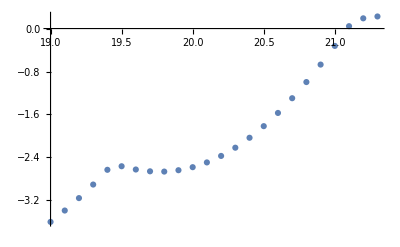

```mathematica
DiscretePlot[eta[b,x[5]]-2*Log[3]/Sqrt[3] Abs[S1hat[x[5],b,x[3]]]+gain[x[5],b]-loss[x[5],b] ,{b,19.0,21.3,0.1},Filling->None]
```

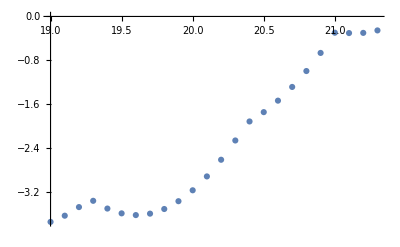

```mathematica
DiscretePlot[eta[b,x[7]]-2*Log[3]/Sqrt[3] Abs[S1hat[x[7],b,x[3]]]+gain[x[7],b]-loss[x[7],b] - 2*Log[5]/Sqrt[5] Abs[S1hat[x[7],b,x[5]]],{b,19.0,21.3,0.1},Filling->None]
```

```mathematica
Stotfourier[bmin_,b_,delta_,t_] := 1/(S1hat[x[7], bmin,delta]-S1hat[x[7], b,delta]) (S1hat[x[7],bmin,delta] S1hat[x[7],b,t] - S1hat[x[7], b, delta] S1hat[x[7],bmin,t]);

etatot[bmin_,b_, delta_] := 1/(S1hat[x[7], bmin,delta]-S1hat[x[7], b, delta]) (S1hat[x[7], bmin,delta] eta[b, x[7]] - S1hat[x[7],b, delta] eta[bmin, x[7]]);

gaincomb[bmin_,b_,delta_] := Stotfourier[bmin,b,delta, x[2]]^2/(2Stotfourier[bmin,b,delta,x[4]])2*Log[2]/Sqrt[4];

losscomb[bmin_,b_,delta_] := MaxValue[{2*Log[2]/Sqrt[4] Stotfourier[bmin,b,delta,x[4]]*(Cos[t]+Stotfourier[bmin,b,delta,x[2]]/(Sqrt[2]Stotfourier[bmin,b,delta,x[4]]))^2,-π< t≤ π},t];


etaplot5[bmin_,b_,delta_]:=etatot[bmin,b,delta] -  2*Log[5]/Sqrt[5] Abs[Stotfourier[bmin,b,delta,x[5]]]+gaincomb[bmin,b,delta] - losscomb[bmin,b,delta];
```

```mathematica
etaplot3[bmin_,b_,delta_]:=etatot[bmin,b,delta] -  2*Log[3]/Sqrt[3] Abs[Stotfourier[bmin,b,delta,x[3]]]+gaincomb[bmin,b,delta] - losscomb[bmin,b,delta];
```

```mathematica
S1hat[x[7], 18.87, x[5]]
S1hat[x[7], 21, x[5]]
```

-0.369112

0.475977

```mathematica
etaplot3[18.87,20.979,x[5]]
```

0.000730003

```mathematica
gaincomb[18.87,21,x[5]] - losscomb[18.87,21,x[5]]
```

-0.74355

```mathematica
losscomb[18.87,21,x[5]]
```

4.60784

```mathematica
2*Log[2]/Sqrt[2] Abs[Stotfourier[18.87,21,x[5],x[2]]]+  2*Log[2]/Sqrt[4] Abs[Stotfourier[18.87,21,x[5],x[4]]]
```

0.74355

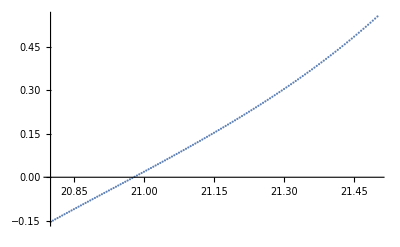

```mathematica
DiscretePlot[etaplot3[18.87,b, x[5]],{b,20.8,21.5,0.005},Filling->None]
```

```mathematica
etaplot3[18.87,20.979, x[5]]
```

0.000730003

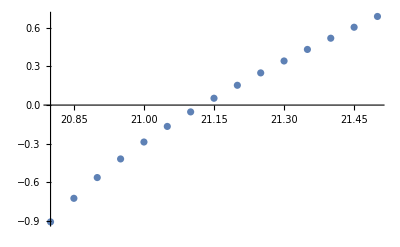

```mathematica
DiscretePlot[etaplot5[18.87,b, x[3]],{b,20.8,21.5,0.05},Filling->None]
```

```mathematica
DiscretePlot[etaplot[18.87,b],{b,20.8,21.5,0.05},Filling->None]
```

-Graphics-